```mathematica
fileName = "/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json";
RadioButtonBar[
Dynamic[fileName],
{
"/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json",
"~/Downloads/optimizerHistory.json"
},Appearance->"Vertical"]

raw=Import[fileName];
```

| /Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json
 | ~/Downloads/optimizerHistory.json

```mathematica
raw= Association[#]&/@raw;
raw=Select[raw,NumericQ[#["maximizeMe"]]&];
```

```mathematica
(*Optional: Drop rows with non-numeric values*)
(*Length[raw]
raw = Select[raw,AllTrue[Values[#],NumericQ]&];
Length[raw]*)
```

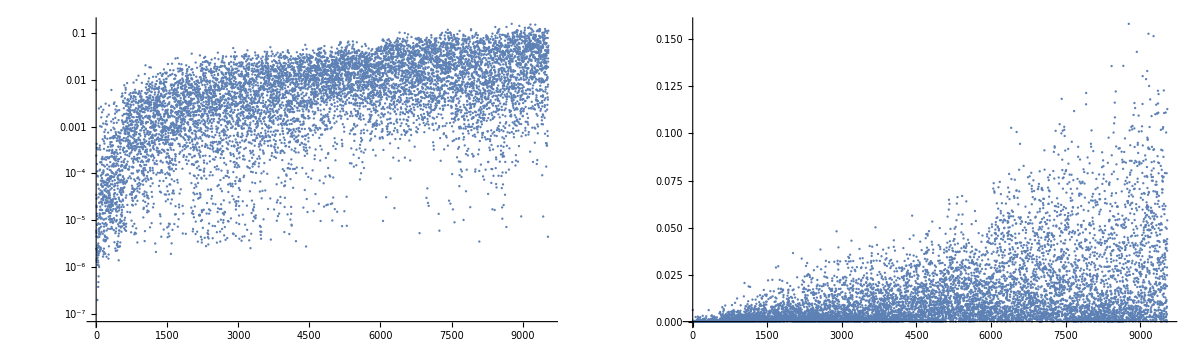

```mathematica
GraphicsGrid[{{
ListLogPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->All,
Joined->False,
ImageSize->600
],
ListPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->{0,All},
Joined->False,
ImageSize->600
]
}},ImageSize->1200]
```

### Live plot

```mathematica
(*Dynamic[livePlot]

makeLivePlot[]:=(
raw=Import[fileName];

raw= Association[#]&/@raw;
raw=Select[raw,NumericQ[#["maximizeMe"]]&];

livePlot = GraphicsGrid[{{
ListLogPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->All,
Joined->False,
ImageSize->600
],
ListPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->{0,All},
Joined->False,
ImageSize->600
]
}},ImageSize->1200];
)

task=CreateScheduledTask[makeLivePlot[],1]; (*Runs myFunction every 1 second*)
StartScheduledTask[task];*)
```

### Analyze

```mathematica
bestCase = MaximalBy[raw,#["maximizeMe"]&][[1]];
```

```mathematica
(*Format for yml*)
string = "";
Do[
string = string<>key<>" : "<>ToString[bestCase[key],CForm]<>"\n",
{key,Keys[bestCase]}
];
string
```

Q1EkG : 110.1948290751
Q2EkG : -155.0395551102
Q3EkG : 131.5102310102
Q4EkG : 95.4097368282
Q5EkG : -27.8919442081
Q6EkG : -120.8627880869
S1ELkG : 1612.1884096474
S2ELkG : -8836.5328416052
S3ELkG : -117.1565057155
S3ERkG : -1716.0221937916
S2ERkG : -12867.7651617124
S1ERkG : 803.0879845597
S1EL_xOffset : 0.0001684404
S1EL_yOffset : 0.0035678324
S2EL_xOffset : 0.0019677676
S2EL_yOffset : 0.001972892
S2ER_xOffset : -0.0004164258
S2ER_yOffset : -0.0024537817
S1ER_xOffset : -0.0035716687
S1ER_yOffset : 0.0031483507
XC1FFkG : 0.6520347832
XC3FFkG : -0.2161436071
YC1FFkG : 0.0833980854
YC2FFkG : -0.0187735642
PDrive_mean_x : -0.0022126167
PDrive_mean_y : 0.0009410151
PDrive_sigma_x : 0.0000346944
PDrive_sigma_y : 0.0000368036
PDrive_mean_xp : 0.0017674136
PDrive_mean_yp : -0.0000918953
PDrive_median_x : -0.0022081899
PDrive_median_y : 0.0009416859
PDrive_median_xp : 0.0017777669
PDrive_median_yp : -0.0000988087
PDrive_sigmaSI90_x : 0.0000287786
PDrive_sigmaSI90_y : 0.0000289085
PDrive_sigmaSI90_z : 0.00011114
PDrive_sigmaSI90_xp : 0.0001003396
PDrive_sigmaSI90_yp : 0.0000462288
PDrive_emitSI90_x : 0.0000556131
PDrive_emitSI90_y : 0.0000244821
PDrive_norm_emit_x : 0.0000659942
PDrive_norm_emit_y : 0.0000401926
PDrive_zCentroid : 991.331941128
PDrive_charge_nC : 1.59968
lostChargeFraction : 0.0002
PDrive_BMAG_x : 1.0402391726
PDrive_BMAG_y : 1.0466733057
sliced_BMAG_x : List(1.1462979892,1.1160986222,1.092690514,1.1948793781,1.123648679)
sliced_BMAG_y : List(1.1818720781,1.0580672236,1.1294943296,1.0864474813,1.1475222866)
errorTerm_lostChargeFraction : 0.
errorTerm_transverseOffset : 0.
errorTerm_angleOffset : 0.
errorTerm_BMAG_rule : 21.7953462101
errorTerm_mainObjective : 21.6084798461
errorTerm_secondaryObjective : 0.8233331942
maximizeMe : 0.1582737874
inputBeamFilePathSuffix : "/beams/2024-10-22_Impact_OneBunch/2024-10-22_oneBunch.h5"
csrTF : False

## Plot all

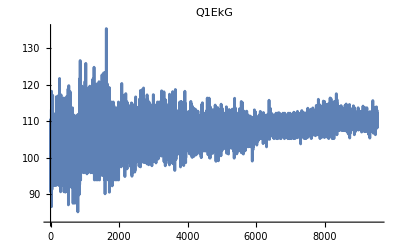
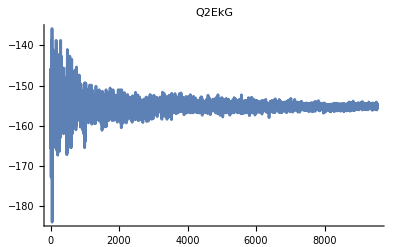
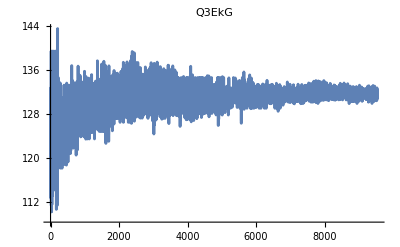
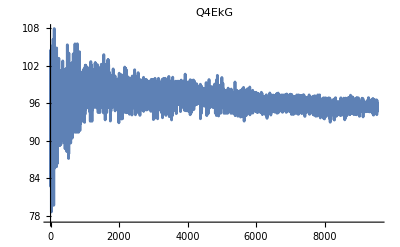
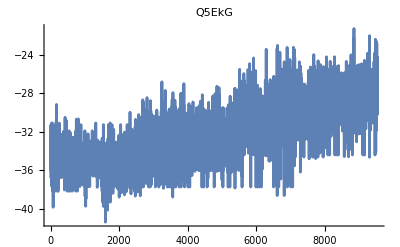
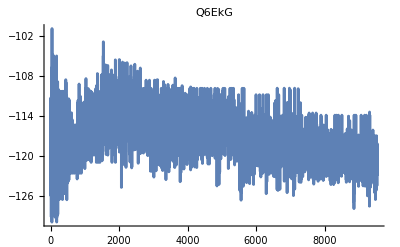
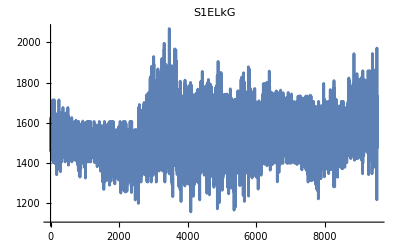
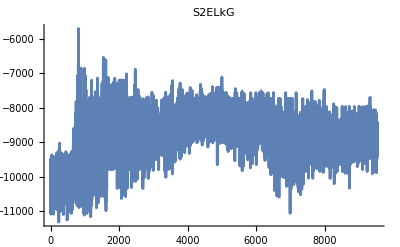
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | 0

```mathematica
imgArr=Table[
ListPlot[
raw[[All,key]],
PlotLabel->key,
ImageSize->400,
LabelStyle->15,
PlotRange->All,
Joined->True
],
{key,Keys[raw[[1]]]}
];

displayCols = 4;
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
]//TableForm
```

## Dump for symbolic regression

Open the CSV in excel, do the automatic suggestion, and resave

```mathematica
Export[
"~/srData.csv",
Dataset[raw]
]
```

~/srData.csv

## Linear model fit

```mathematica
freeVars=Intersection[
Keys[raw[[1]]],
{"QA10361kG","QA10371kG","QE10425kG","QE10441kG","QE10511kG","QE10525kG","L0BPhaseSet","L1PhaseSet","L2PhaseSet","L3PhaseSet","Q1EkG","Q2EkG","Q3EkG","Q4EkG","Q5EkG","Q6EkG","S1ELkG","S2ELkG","S3ELkG","S3ERkG","S2ERkG","S1ERkG","S1EL_xOffset","S1EL_yOffset","S2EL_xOffset","S2EL_yOffset","S2ER_xOffset","S2ER_yOffset","S1ER_xOffset","S1ER_yOffset","Q5FFkG","Q4FFkG","Q3FFkG","Q2FFkG","Q1FFkG","Q0FFkG", "XC1FFkG","XC3FFkG","YC1FFkG","YC2FFkG"}
]
(*Mathematica doesn't like underscores...*)
freeVarsMathematica=StringReplace[#,"_"->""]&/@freeVars;
```

{Q1EkG,Q2EkG,Q3EkG,Q4EkG,Q5EkG,Q6EkG,S1ELkG,S1EL_xOffset,S1EL_yOffset,S1ERkG,S1ER_xOffset,S1ER_yOffset,S2ELkG,S2EL_xOffset,S2EL_yOffset,S2ERkG,S2ER_xOffset,S2ER_yOffset,S3ELkG,S3ERkG,XC1FFkG,XC3FFkG,YC1FFkG,YC2FFkG}

```mathematica
fitVar = "PDrive_twiss_beta_x"
(*fitVar = "bunchSpacing"*)
```

PDrive_twiss_beta_x

```mathematica
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVarsMathematica,
Symbol[#]&/@freeVarsMathematica
]
```

LinearModelFit::desmat: Unable to construct a numeric design matrix. Nominal variables may need to be specified, or non-numeric entries for numeric variables may need to be replaced.

```mathematica
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
AspectRatio->Automatic,
Frame->True,
FrameLabel->{"Actual","Predicted"}
]
```

-Graphics-

```mathematica
lm["ANOVATable"]
```

### Fit all dependent vars

```mathematica
allFitVars  = Complement[
Keys[raw[[1]]],
freeVars
];
```

```mathematica
(*
imgArr=Table[
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVarsMathematica,
Symbol[#]&/@freeVarsMathematica
];

Show[
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
Frame->True,
FrameLabel->{"Actual","Predicted"},
PlotLabel->Row[{fitVar,": ",Style[ToString[lm["RSquared"]],ColorData["Rainbow"][lm["RSquared"]]]}],
ImageSize->400,
AspectRatio->1,
LabelStyle->15,
PlotRange->All
],
Plot[x,{x,Min[lm["Response"]],Max[lm["Response"]]},PlotStyle->Red]
],
{fitVar,allFitVars}
];*)
```

```mathematica
(*displayCols = 4;
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
]//TableForm*)
```

## Parse JSON strings to assoc

```mathematica
(*This is a stupid trick, but ensures numbers in scientific notation are interpreted correctly: https://mathematica.stackexchange.com/questions/15051/reading-in-scientific-notation-from-c-to-mathematica*)
stringToNumber[string_]:=ImportString[string,"Table"][[1,1]]
```

```mathematica
jsonTextToAssoc[string_]:=(
stringParts = StringSplit[StringDelete[#,WhitespaceCharacter],":"]&/@StringSplit[string,"\n"];
Association[#[[1]]->stringToNumber[#[[2]]]&/@stringParts]
)
```

```mathematica
tmp="L0BPhaseSet : -1.7210344516
L1PhaseSet : -20.3120443443
L2PhaseSet : -38.6737055166
L3PhaseSet : -1.4632882388
S1EL_xOffset : 0.0003852549
S1EL_yOffset : -0.0002411137
S2EL_xOffset : -0.0014178669
S2EL_yOffset : 0.0000111705
S2ER_xOffset : -0.002238162
S2ER_yOffset : -0.0006759962
S1ER_xOffset : 0.0010071369
S1ER_yOffset : 0.0003984557
XC1FFkG : 0.2064553639
XC3FFkG : -0.089916372
YC1FFkG : -0.0022311951
YC2FFkG : -0.0085115845";
```

```mathematica
priorSettings = jsonTextToAssoc[tmp]
```

<|L0BPhaseSet→-1.72103,L1PhaseSet→-20.312,L2PhaseSet→-38.6737,L3PhaseSet→-1.46329,S1EL_xOffset→0.000385255,S1EL_yOffset→-0.000241114,S2EL_xOffset→-0.00141787,S2EL_yOffset→0.0000111705,S2ER_xOffset→-0.00223816,S2ER_yOffset→-0.000675996,S1ER_xOffset→0.00100714,S1ER_yOffset→0.000398456,XC1FFkG→0.206455,XC3FFkG→-0.0899164,YC1FFkG→-0.0022312,YC2FFkG→-0.00851158|>

```mathematica
TableForm[
Table[
{
key,priorSettings[key],bestCase[key],bestCase[key]-priorSettings[key]
},
{key,Keys[priorSettings]}
],
TableHeadings->{None,{
Style["Parameter",Bold],
Style["150 μm spacing",Bold],
Style["New spacing",Bold],
Style["Delta",Bold]}}
]
```

Parameter | 150 μm spacing | New spacing | Delta
L0BPhaseSet | -1.72103 | Missing[KeyAbsent,L0BPhaseSet] | 1.72103+Missing[KeyAbsent,L0BPhaseSet]
L1PhaseSet | -20.312 | Missing[KeyAbsent,L1PhaseSet] | 20.312+Missing[KeyAbsent,L1PhaseSet]
L2PhaseSet | -38.6737 | Missing[KeyAbsent,L2PhaseSet] | 38.6737+Missing[KeyAbsent,L2PhaseSet]
L3PhaseSet | -1.46329 | Missing[KeyAbsent,L3PhaseSet] | 1.46329+Missing[KeyAbsent,L3PhaseSet]
S1EL_xOffset | 0.000385255 | 0.00016844 | -0.000216815
S1EL_yOffset | -0.000241114 | 0.00356783 | 0.00380895
S2EL_xOffset | -0.00141787 | 0.00196777 | 0.00338563
S2EL_yOffset | 0.0000111705 | 0.00197289 | 0.00196172
S2ER_xOffset | -0.00223816 | -0.000416426 | 0.00182174
S2ER_yOffset | -0.000675996 | -0.00245378 | -0.00177779
S1ER_xOffset | 0.00100714 | -0.00357167 | -0.00457881
S1ER_yOffset | 0.000398456 | 0.00314835 | 0.0027499
XC1FFkG | 0.206455 | 0.652035 | 0.445579
XC3FFkG | -0.0899164 | -0.216144 | -0.126227
YC1FFkG | -0.0022312 | 0.0833981 | 0.0856293
YC2FFkG | -0.00851158 | -0.0187736 | -0.010262